### two-photon rabi flopping

P. Huft

## global definitions

```mathematica
Clear["Global`*"]
```

```mathematica
(*get from local files*)
SetDirectory[NotebookDirectory[]];
<<"rbconsts.m"
<<"physconsts.m"

(*FUNCTIONS*)

BuildSchroedingerSystem[H_,psi0_]:=Module[
{hamiltonian=H,ψ0=psi0,ψ,statelength,eqs,ics,sys,P,i},
statelength = Length[ψ0];
ψ = Array[Subscript[P, #][t]&,statelength];
eqs = {};(*system to solve*)
ics = {};(*initial conditions*)
For[i=1,i<statelength+1,i++,
AppendTo[eqs,D[ψ[[i]],t]==-ⅈ (hamiltonian.ψ)[[i]]];
AppendTo[ics,(ψ[[i]]/.t->0)==ψ0[[i]]];
];
sys = Flatten@Join[eqs,ics];
{ψ,sys}
]

gJ[L_,J_]:=gL(J(J+1)+L(L+1)-S(S+1)
+gS(J(J+1)-L(L+1)+S(S+1)))/(2J(J+1));
gF[J_,F_]:= (gJ(F(F+1)+J(J+1)-INuc(INuc+1))
+gI(F(F+1)-J(J+1)+INuc(INuc+1)))/(2F(F+1));

(*Zeeman shifts, only for diagonal elements*)
FZeemanMatElem[L_,{J_,mJ_},{JJ_,mJJ_},Bz_]:=KroneckerDelta[mJ,mJJ] μB gJ[L,J]mJ Bz;
HFZeemanMatElem[I_,L_,J_,{F_,mF_},{FF_,mFF_},Bz_]:=KroneckerDelta[mF,mFF]μB Bz (ClebschGordan[{F,mF},{1,0},{FF,mFF}] √(2 F +1)(-1)^(1+J+I)(gJ[L,J] (-1)^F √(J (J+1)(2 J+1))SixJSymbol[{J,I,F},{FF,1,J}]+
gI(-1)^FF √(I(I+1)(2I+1))SixJSymbol[{I,J,F},{FF,1,I}]));

(*prob of speed v at temp T*)
MaxBoltzDist[T_,v_]:=PDF[MaxwellDistribution[√((kB T)/mRb)],v];

MaxBoltzSpeedSample[T_,speedband_,samples_]:=Module[
{fmax,y,v,vdomain=speedband,f=0,flist={},vlist={},ylist={},samps=0},
fmax=MaxBoltzDist[T,√((kB T)/mRb)]; 
While [samps<samples,
v = (vdomain[[2]]-vdomain[[1]])RandomReal[];
f =MaxBoltzDist[T,v];
y=fmax RandomReal[];
If[y≤f,
AppendTo[ylist,y];(*prob that y<=f is prob that speed is measured*)
AppendTo[vlist,v];(*speeds*)
AppendTo[flist,f];(*probabilities*)
samps++;
];
];
{vlist,ylist,flist}
];

MaxBoltzVelocitySample[T_,speedband_,samples_]:=Module[{velocityList={},ex,ey,ez,v,A},
For[n=1,n<samples+1,n++,
ex=2 RandomReal[]-1;
ey=2 RandomReal[]-1;
ez=2 RandomReal[]-1;
v=MaxBoltzSpeedSample[T,speedband,1][[1,1]];
A=√(ex^2+ey^2+ez^2);
AppendTo[velocityList,{ex v/A,ey v/A,ez v/A}];
];
velocityList
];
```

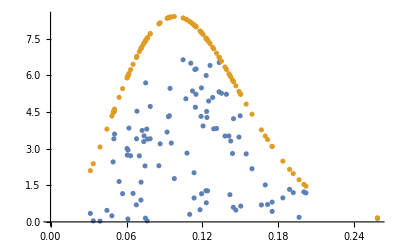

```mathematica
(*test Maxwell-Boltzmann sampling*)
{v,y,f}=MaxBoltzSpeedSample[5*^-5,{0,1},100];
ListPlot[{Transpose@{v,y},Transpose@{v,f}}]
```

```mathematica
MaxBoltzVelocitySample[5*^-5,{0,1},10]
```

## simple Rabi oscillation test

```mathematica
(*single atom Hamiltonian with effective basis {g,e}*)
Clear[Ω1,Ω2,Δ1,Δ2];
scl = 1*^9;
numStates=3; (*single atom states*)
numAtoms =1;
atomBasis = IdentityMatrix[numStates];
(*rabi frequencies and AC stark shifts calculated in rydberg_rabi.ipynb*)
Ω1=695214755.6324366; 
Ω2 = 71550273.89520717;
ΩEff = 2π*600099;
Δ1 = -13194689145.077131;
Δ2 =-Δ1;
diffACStarkHFge =1298349.0058336519;
diffACStarkHFer=339133.4042641225;
(*Haf=({{0, Ω1/2, 0}, {Ω1/2, Δ1 +diffACStarkHFge, Ω2/2}, {0, Ω2/2, (Δ1+diffACStarkHFge + Δ2 +diffACStarkHFer)}})/scl;*)
scl=1;
Ω1 = 1;Ω2=0.3;Δ1=20Ω1;Δ2=-Δ1;Γ=0;(*diagnostics, e.g. reproduce Shore examples*)

Haf=({{0, Ω1/2, 0}, {Ω1/2, Δ1, Ω2/2}, {0, Ω2/2, Δ1+Δ2+ⅈ Γ/2}})/scl;
ΩEff = Ω1 Ω2/(2Δ1);

(*assume real Rabi freq.*)
(*scl=1;
Haf=({{0, /2, 0}, {1/2, 0, 1/2}, {0, 1/2, 0}});(*Shore, page 794 Fig. 13.3-1*)
ΩEff = 1/(2*5);*)
Haf//MatrixForm
```

(0 | 1/2 | 0
1/2 | 20 | 0.15
0 | 0.15 | 0)

Time to run sim: 0 mins

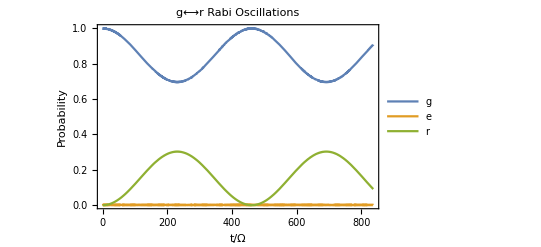

```mathematica
(*Build the initial array state and eqs to solve*)
ψ0 = ConstantArray[0,numAtoms numStates];
ψ0[[1]]=1;(*start with all atoms in ground state*)
tmax=2π scl/ΩEff;
{ψ,sys}=BuildSchroedingerSystem[Haf,ψ0];
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,0,tmax},Method->"BDF"]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[soln[[i,2]],{i,Range[Length[soln]]}];
leg = {"g","e","r"};
plt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2},{t,0,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["g⟷r Rabi Oscillations"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]
```

## frequency scan

Add in finite temperature and beam profiles next, then do several runs and average

```mathematica
(*single atom Hamiltonian with effective basis {g,e}*)
Clear[Ω1,Ω2,Δ1,Δ2];
scl = 1*^9;
numStates=3; (*single atom states*)
numAtoms =1;
atomBasis = IdentityMatrix[numStates];
(*rabi frequencies and AC stark shifts calculated in rydberg_rabi.ipynb*)
Ω1=2π*102712885; 
Ω2 = 2π*24538455;
Δ1 = -2π*2100000000;
Δ2 =-Δ1;
ΩEff = Ω1 Ω2/(2Abs[Δ1]); 
diffACStarkHFge =1298349.0058336519;
diffACStarkHFer=339133.4042641225;
Bbias = 3*10^-4 ;(*magnetic bias field [T]*)
diffZ1ge =(HFZeemanMatElem[INuc,1,3/2,{3,1},{3,1},Bbias]-HFZeemanMatElem[INuc,0,1/2,{2,0},{2,0},Bbias])/ℏ;
diffZ1er =(FZeemanMatElem[2,{5/2,5/2},{5/2,5/2},Bbias]-HFZeemanMatElem[INuc,1,3/2,{3,1},{3,1},Bbias])/ℏ;
diffShiftge =diffACStarkHFge + diffZ1ge;
diffShifter =diffACStarkHFer + diffZ1er;
```

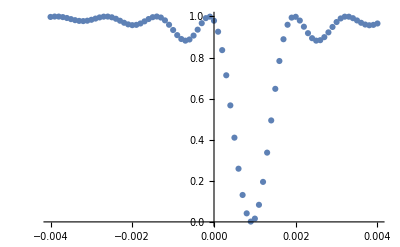

```mathematica
(*Build the initial array state and eqs to solve*)
ψ0 = ConstantArray[0,numAtoms numStates];
ψ0[[1]]=1;(*start with all atoms in ground state*)
tmax=π scl/ΩEff;
stepmax =4;
stepmin = -4;
stepsize = .1;
steps =Range[stepmin,stepmax,stepsize];
fSteps = Table[2π fMHz*1*^6,{fMHz,steps}];
solnList = {};
endPts = {};
For[i=1, i<Length[fSteps]+1,i++,
(*add finite atom temp and addressing beam intensity profiles*)
Haf=({{0, (Ω1/2), 0}, {(Ω1/2), Δ1 + diffACStarkHFge +fSteps[[i]], (Ω2/2)}, {0, (Ω2/2), Δ1+diffACStarkHFge + Δ2 +diffACStarkHFer+ fSteps[[i]]}})/scl;
{ψ,sys}=BuildSchroedingerSystem[Haf,ψ0];
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,0,tmax}]];
If[Length[steps]<20,
Print[StringForm["step ``, `` mins",i,If[time>60,Floor[time/60//N],NumberForm[time/60//N,2]]]]
];
AppendTo[endPts,soln[[1,2]]/.t-> tmax];
]
populationData = Transpose@{fSteps/(2π scl),Abs[endPts]^2};
ListPlot[populationData,PlotRange->{0,1}]
```

```mathematica
(Δ1+diffACStarkHFge + Δ2 +diffACStarkHFer)/(2π scl)
```

0.000260613

step 0, 0.0083 mins

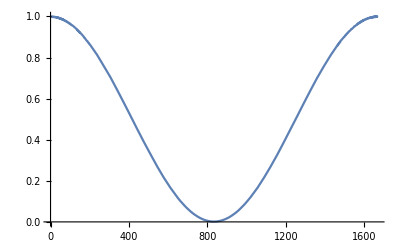

```mathematica
fRedDetuning =2π scl  Sort[populationData,#1[[2]]<#2[[2]]&][[1,1]] ;
ψ0 = ConstantArray[0,numAtoms numStates];
ψ0[[1]]=1;(*start with all atoms in ground state*)
tmax=2π scl/ΩEff;
Haf=({{0, Ω1/2, 0}, {Ω1/2, Δ1 +diffACStarkHFge + fRedDetuning, Ω2/2}, {0, Ω2/2, Δ1+diffACStarkHFge + Δ2 +diffACStarkHFer+ fRedDetuning}})/scl;
{ψ,sys}=BuildSchroedingerSystem[Haf,ψ0];
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,0,tmax}]];
Print[StringForm["step ``, `` mins",0,If[time>60,Floor[time/60//N],NumberForm[time/60//N,2]]]]
Plot[Abs[soln[[1,2]]]^2,{t,0,tmax},PlotRange->{0,1}]
```

```mathematica
scl 2π/ΩEff//N
```

1666.39

```mathematica
Plot[Table[Abs[solnList[[i]]]^2,{i,1,Length[solnList]}],{t,0,tmax}]
```

$Aborted

```mathematica
curves = {};
For[i=1,i<Length[solnList]+1,i++,

]
```

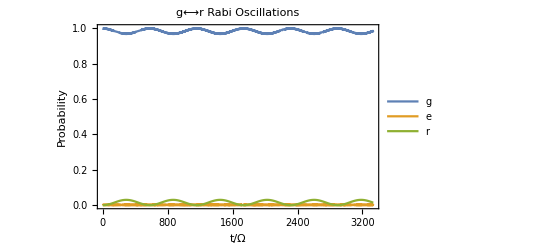

{-5,-4,-3,-2,-1,0,1,2,3,4,5}

```mathematica
leg = {"g","e","r"};
plt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2},{t,0,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["g⟷r Rabi Oscillations"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]
(*Export[ToString[StringForm["plot_rabi_flop_``atoms_``states_blockaded``.png",numAtoms,numStates,ΩB/Ω]],plt]*)
```